# Project 3 - Graph Application

## IX1500

## Task Level C: Routing

Every city listed below represents a router that forwards packet to their final destination. The weight (cost) between two linked cities is assumed to be inversely proportional to the free capacity of the link.

This task is about creating an optimal tree so that each router can be accessed with minimal weight. The tree should show how data packets are routed so that each city can be reached by the information flow that is based on Stockholm.

```mathematica
city={"Abisko","Boden","Falun","Goteborg","Hoganas","Hudiksvall","Jonkoping","Kalmar","Kiruna","Lidkoping","Linkoping","Lulea","Lund","Malmo","Mariestad","Ostersund","Stockholm","Strangnas","Timra","Uppsala","Umea","Varberg","Visby"};
```

```mathematica
links={{15,18},{13,17},{3,16},{6,3},{18,6},{12,2},{15,11},{19,21},{7,8},{19,2},{7,4},{21,17},{17,11},{23,11},{10,7},{16,17},{10,20},{13,5},{3,17},{7,22},{15,10},{16,18},{11,16},{17,23},{18,17},{20,6},{11,7},{9,2},{3,20},{4,17},{19,17},{7,20},{22,4},{14,7},{15,17},{6,17},{20,5},{16,15},{11,3},{9,1},{4,10},{5,14},{6,16},{16,19},{13,8},{8,23},{16,10},{4,13},{2,16},{15,3},{20,18}};
```

The list above shows how every city is linked (has an edge) to one or more cities.

## Generate weight for every link

```mathematica
genWeight[e_, c_]:=
Module[{edgeWeight  = {}, capacity, i},
For[i=0, i<Length[e], i++,
capacity = RandomInteger[{1,5}];
AppendTo[edgeWeight, c/capacity];
];
edgeWeight
]
```

```mathematica
constant = 1;
```

```mathematica
w = genWeight[links, constant]
```

{1,1/4,1/5,1,1/5,1/4,1,1,1,1/3,1/4,1,1/5,1/2,1/5,1/4,1/4,1/3,1/4,1/5,1/2,1/2,1/4,1/5,1/5,1,1,1/3,1/5,1/4,1/4,1/5,1/3,1/3,1/4,1/4,1/3,1/5,1,1/5,1/2,1,1/3,1/3,1/3,1/2,1/4,1/4,1/5,1/5,1/5}

Specific edge-weights.

Stockholm | – | Göteborg | 25
Stockholm | – | Lund | 25
Göteborg | – | Lund | 25
Stockholm | – | Falun | 15
Falun | – | Östersund | 15

```mathematica
w[[15]] = constant/25;
w[[39]] = constant/25;
w[[14]] = constant/25;
w[[10]] = constant/15;
w[[9]] = constant/15;
```

## Construct a graph from adjacency matrix

Create a graph with the provided adjacency matrix and position the vertexes according to the provided  city coordinates.

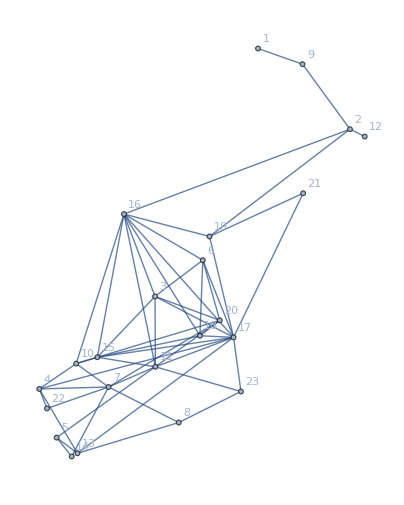

```mathematica
𝒢=AdjacencyGraph[𝔸,VertexCoordinates->(Reverse/@𝕔),VertexLabels->Automatic,EdgeWeight->w]
```

## Find shortest path spanning tree

```mathematica
g = FindShortestPath[𝒢,17,All, Method-> "Dijkstra"];
```

```mathematica
edges = {};
```

A function that creates a tree with shortest path from root vertex to every other vertexes.

```mathematica
FShortestPath[c_, l_, g_] :=
Module[{edges = {}, ind,i  ,k, val},
For[i= 1, i < Length[c]+1, i++,
ind = g[i];
For[k = 1, k  < Length[ind], k++,
val = {ind[[k]], ind[[k+1]]};
If[MemberQ[edges, val], , AppendTo[edges, val];
]]
];
edges
];
```

```mathematica
edges = FShortestPath[city, links,g]
```

{{17,19},{19,2},{2,9},{9,1},{17,3},{17,4},{17,13},{13,5},{3,6},{4,10},{10,7},{13,8},{17,11},{2,12},{5,14},{3,16},{16,15},{16,18},{3,20},{17,21},{4,22},{17,23}}

## Shortest path spanning

Create and draw a graph from the matrix containing the shortest path spanning tree.

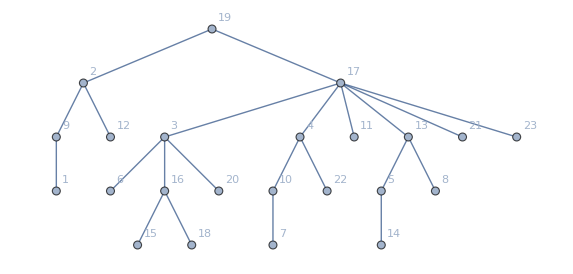

```mathematica
shortestPathTree=AdjacencyGraph[An,VertexLabels->Automatic]
```

## Illustrate the tree with the map of Sweden

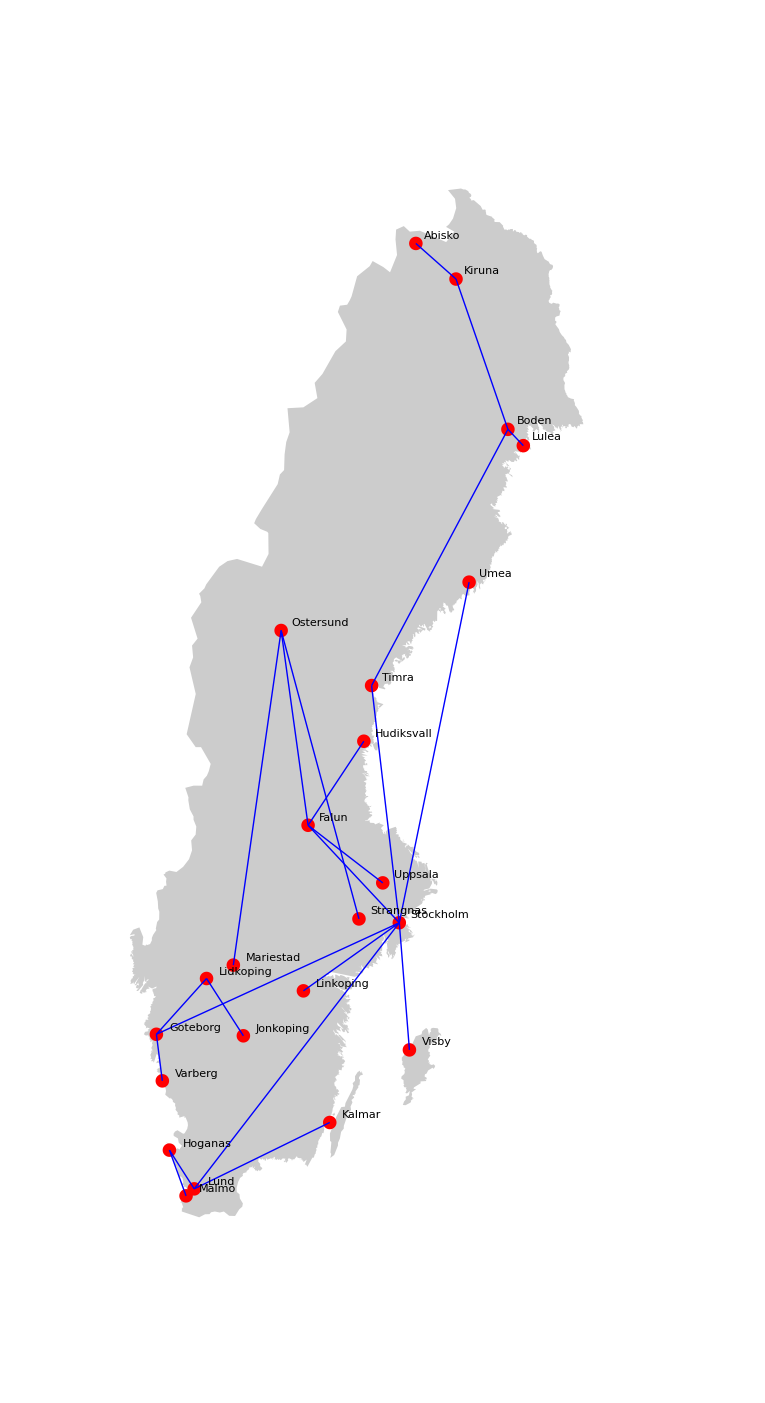

```mathematica
GeoGraphics[{
Polygon[CountryData["Sweden"]],
geoGraph[v,edges,𝕔,r,EdgeStyle->Blue,VertexStyle->GeoStyling[Red],VertexLabels->city]
},GeoBackground->None,GeoProjection->"LambertAzimuthal"]
```

## If the link between Stockholm and Lund stop working

```mathematica
dG =EdgeDelete[𝒢, 13<->17];
```

Construct an alternative shortest path spanning tree while the Stockholm - Lund link is removed.

```mathematica
g2 = FindShortestPath[dG,17,All];
```

```mathematica
edges2 = FShortestPath[city, links,g2]
```

{{17,19},{19,2},{2,9},{9,1},{17,3},{17,4},{4,13},{13,5},{3,6},{4,10},{10,7},{13,8},{17,11},{2,12},{5,14},{3,16},{16,15},{16,18},{3,20},{17,21},{4,22},{17,23}}

Draw the alternative tree with the map of Sweden.

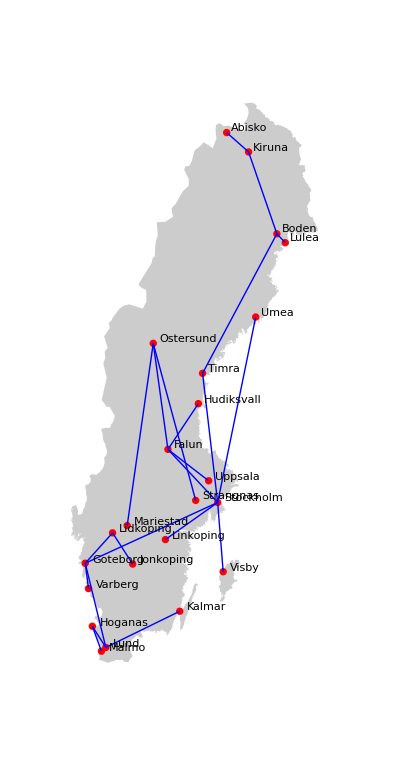

```mathematica
GeoGraphics[{
Polygon[CountryData["Sweden"]],
geoGraph[v,edges2,𝕔,r,EdgeStyle->Blue,VertexStyle->GeoStyling[Red],VertexLabels->city]
},GeoBackground->None,GeoProjection->"LambertAzimuthal"]
```